### Figures for oriented areas (squares and parallelograms)

```mathematica
<<peeters` ;
peeters`setGitDir[ "../project/figures/GAelectrodynamics" ]
```

/Users/pjoot/project/figures/GAelectrodynamics

```mathematica
ClearAll[o, e1, e2, bold, sz, fs, tsub, midpoint, midtext, shift, sep, orientedArc]
o = {0,0};
e2 = {0,1};
e1 = {1,0};
bold = Style[ #, Bold] &;
sz = 14;
fs = Style[ #, FontSize-> sz] &;
tsub[t_,s_] := Subscript[bold[t]// fs,s];
esub := tsub[e, #]&;
vsub := tsub[v, #]&;
midpoint[p_] := (p[[1]] + p[[2]])/2 ;
midtext[p_, sh_,text_] := Text[text,midpoint[p] + sh]
orientedArc[s_, f_, r_,c_] := Module[{data,p},
data=Table[r{Cos[x],Sin[x]},{x,s,f, (f-s)/100}];p=ListPlot[data,Frame->True,Axes->False,Joined->True,PlotStyle->{c,Thick}, AspectRatio->1];
p/.Line[x_]:>{Arrowheads[{0,.05(*,.05*),0}],Arrow[x]}
];

shift = -0.06;
sep = 1.5 e1;


ClearAll[parallelogram]

(*fixme: use orientedArc here to make the arrow head line up with the curve better*)
parallelogram[v1_,v2_,ori_,l1_,l2_, c1_, c2_, orientation_]:= Module[{m,r},
m = midpoint[{v1,v2}];
r= Min[
Norm[0.7 (m-v1/2)],
Norm[0.7 (m-v2/2)]];
{Thick,c1,
Arrowheads[0.05],Arrow[{{ori,ori+v1},{ori+v1,ori+v1+v2},{ori+v1+v2,ori+v2},{ori+v2,ori}}],
Black,
midtext[{ori,ori+v1},-shift v2,l1],
midtext[{ori+v1,ori+v1+v2},shift v1,l2],
c2,
Circle[
m + ori,
r,
{0,2 Pi 0.9}],
Arrow[{m+ ori +r e2 -orientation shift e1/2,m+ori +r e2+orientation shift e1/2}]
}];
```

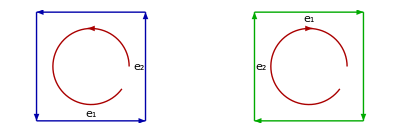

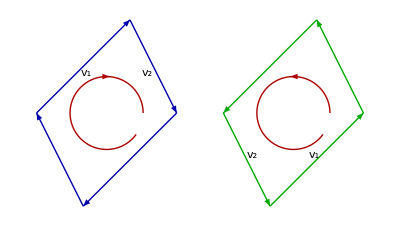

```mathematica
p1 = Graphics[ 
Flatten[
{
parallelogram[e1, e2, o, tsub[e,1], tsub[e,2], Blue//Darker, Red // Darker,1],
parallelogram[e2,e1, 2e1, tsub[e,2], tsub[e,1], Green//Darker, Red // Darker,-1]
}
,1
]]

p2 = Graphics[ 
Flatten[
{
parallelogram[e1+e2, e1/2-e2, o,  tsub[v,1], tsub[v,2], Blue//Darker, Red // Darker,-1],
parallelogram[e1/2-e2,e1+e2, 2e1, tsub[v,2], tsub[v,1], Green//Darker, Red // Darker,1]
}
,1
]]
```

```mathematica
peeters`exportForLatex["orientedAreasFig1", p1]
peeters`exportForLatex["orientedParallelogramFig1", p2]
```

{orientedAreasFig1.eps,orientedAreasFig1pn.png}

{orientedParallelogramFig1.eps,orientedParallelogramFig1pn.png}

### Figures for 90 degree rotations.

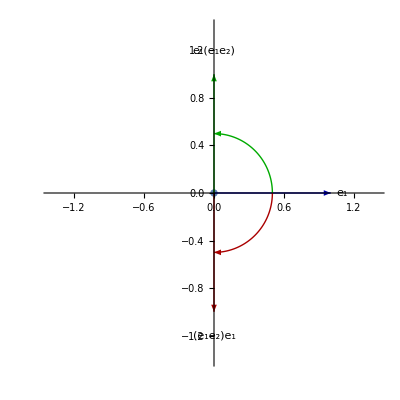

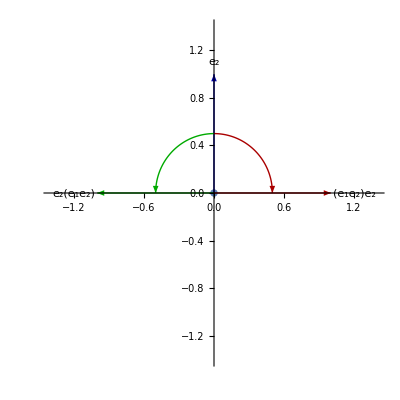

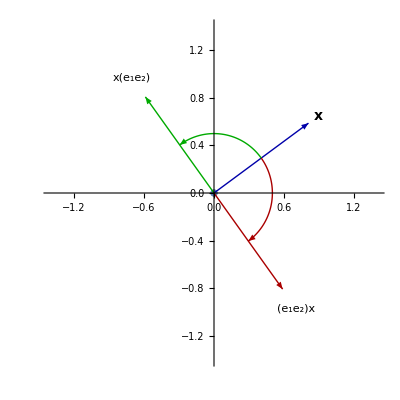

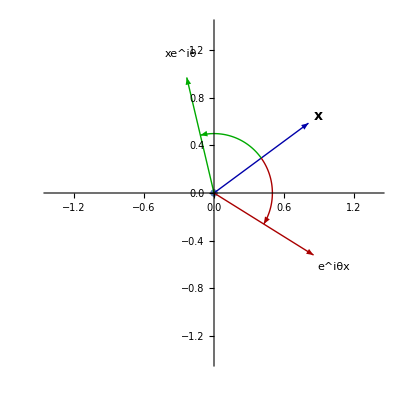

```mathematica
rotatedVectorPlot[rn_,th_,th2_,lab_, rot_] := Module[{c1, v1, v2, v0},
c1= Blue//Darker;
v1 = e1 Cos[th] + e2 Sin[th];
v2 = e1 Cos[th + th2] + e2 Sin[th +th2];
v0 = e1 Cos[th - th2] + e2 Sin[th -th2];
Show[
ListPlot[{o}, AspectRatio->1, PlotRange->{{-rn,rn},{-rn, rn}}],
Graphics[
{
Thick,c1,
Arrowheads[0.05],
Arrow[{o, v1}],
Green//Darker,
Arrow[{o, v2}],
Red//Darker,
Arrow[{o, v0}],
Black,
Text[lab,v1*1.1],
Text[Row[{lab,rot}// Flatten],v2*1.2],
Text[Row[{rot, lab}// Flatten],v0*1.2]
}
] (*Graphics*),
orientedArc[ th,th+th2, 0.5, Green//Darker],
orientedArc[th, th-th2,0.5, Red//Darker]
]
]
p3 =rotatedVectorPlot[1.4,0,Pi/2,esub[1], {"(",esub[1],esub[2],")"}]
p4 =rotatedVectorPlot[1.4,Pi/2,Pi/2,esub[2], {"(",esub[1],esub[2],")"}]
p5 =rotatedVectorPlot[1.4,Pi/5,Pi/2,bold[x]//fs, {"(",esub[1],esub[2],")"}]
p6 =rotatedVectorPlot[1.4,Pi/5,3Pi/8,bold[x]//fs, {e^iθ// fs}]
```

```mathematica
(*peeters`exportForLatex["rotationOfe1Fig1", p3]
peeters`exportForLatex["rotationOfe2Fig1", p4]*)
(*peeters`exportForLatex["rotationOfVFig1", p5]*)
peeters`exportForLatex["rotationOfXFig1", p6]
```

{rotationOfXFig1.eps,rotationOfXFig1pn.png}

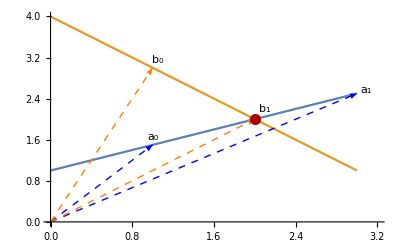

```mathematica
ClearAll[ps]
ps =Module[{f,g, a0, a1, b0, b1,inter, p, tval},
f = #/2 + 1 &;
g = -# +4 &;
a0 = {1,f[1]};
a1 = {3,f[3]};
b0 = {1,g[1]};
b1 = {2,g[2]};
inter = Solve[ a0 + s(a1-a0) == b0 + t(b1-b0),{s,t}];
tval = (t/.inter // Flatten)// First;
p = b0 + tval(b1-b0);
Show[
Plot[{f[x],g[x]},{x,0,3}, PlotRange->{{0,3.2},{0,4}}],
Graphics[
{
Blue 
,Dashed
,Arrowheads[0.03]
,Arrow[{o,a0}]
,Arrow[{o,a1}]
,Orange 
,Arrow[{o,b0}]
,Arrow[{o,b1}]
,Black
, Text[ tsub[a,0], a0*1.1-0.1e1]
, Text[ tsub[a,1], a1*1.03]
, Text[ tsub[b,0], b0*1.05]
, Text[ tsub[b,1], b1*1.05+0.1e2]
, Red // Darker
, PointSize[0.02]
, Point[ p ]
}
] (*Graphics*)
] (*Show*) 

]
```

```mathematica
peeters`exportForLatex["intersectionOfLinesFig1", ps]
```

{intersectionOfLinesFig1.eps,intersectionOfLinesFig1pn.png}